```mathematica
DENS = 921 ; (*kg/m^3 *)
SPEC= 2100; (* J/kgK *)
k = 2.0 ;(*w/mk*)
ALPHA = k/(DENS*SPEC);

LC1= 0.001 ;(* meters **)
LC2=0.01;
LC3 = 0.1;

h = 200 ; (*200 W/m^2K*)

BiA= 0.1;
BiB = 1.0;
BiC=10.0;

(* From I+D Table 5.1 - 3rd Edition *)
C1A=1.016;
C1B=1.1191;
C1C= 1.2620;

ETA1A= 0.311;
ETA1B = 0.8603;
ETA1C=1.4289;


(*  LC1, BiA and C1A Problem    *)
```

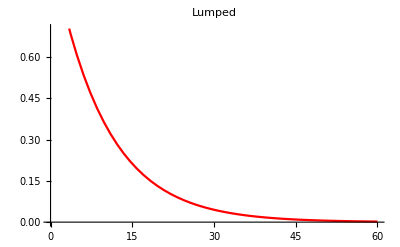

```mathematica
TIME = 60;
FO = (ALPHA*TIME)/(LC1^2);
ARG = (ETA1A^2)*FO;
THETA  = C1A*Exp[-(ETA1A^2)*((ALPHA*TIME)/(LC1^2))];
Plot2  = Plot [Exp[-BiA*(ALPHA*x)/(LC1^2)],{x,0,60},PlotStyle->Red,PlotLabel-> "Lumped"]
```

```mathematica
(*           LUMPED             *)
(* THETALUMPED = Exp[-BiA*FO]   *)

(*Plot1 = Plot[C1A*Exp[-(ETA1A^2)*((ALPHA*x)/(LC1^2))],{x,0,60},PlotStyle->Blue];
Plot2  = Plot [Exp[-BiA*(ALPHA*x)/(LC1^2)],{x,0,60},PlotStyle->Red];
Show[Plot1, Plot2,AxesLabel->{"time","θ"}]
FOss = - Log[0.01/C1A]/(ETA1A^2)
tss = FOss* LC1^2/ALPHA


TIME = 600;
FO = (ALPHA*TIME)/(LC2^2);
ARG = (ETA1B^2)*FO;
THETA  = C1B*Exp[-(ETA1B^2)*((ALPHA*TIME)/(LC2^2))];

Plot1= Plot[C1B*Exp[-(ETA1B^2)*((ALPHA*x)/(LC2^2))],{x,0,600},PlotStyle->Blue];
Plot2  = Plot [Exp[-BiB*(ALPHA*x)/(LC2^2)],{x,0,600},PlotStyle->Red];
Show [Plot1, Plot2,AxesLabel->{"time","θ"}]
FOss = - Log[0.01/C1B]/(ETA1B^2)
tss = FOss* LC2^2/ALPHA

*)
```

2.27496

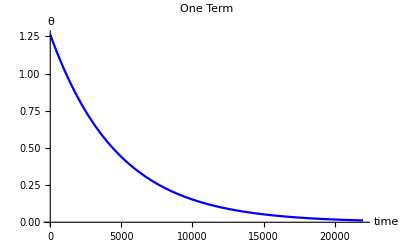

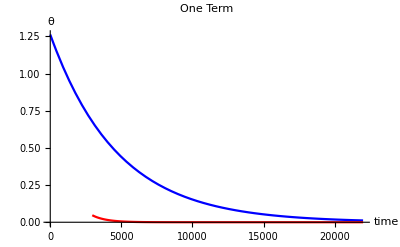

2.36947

22913.9

2.36947

22913.9

```mathematica
TIME = 22000;
FO = (ALPHA*TIME)/(LC3^2)
ARG = (ETA1C^2)*FO;
THETA  = C1C*Exp[-(ETA1C^2)*((ALPHA*TIME)/(LC1^2))];

Plot1 = Plot[C1C*Exp[-(ETA1C^2)*((ALPHA*x)/(LC3^2))],{x,0,22000},PlotStyle->Blue,AxesLabel->{"time","θ"},PlotLabel->"One Term"]
Plot2  = Plot [Exp[-BiC*(ALPHA*x)/(LC3^2)],{x,0,22000},PlotStyle->Red];
Show [Plot1, Plot2,AxesLabel->{"time","θ"}]
FOss = - Log[0.01/C1C]/(ETA1C^2)
tss = FOss* LC3^2/ALPHA
```

```mathematica
(* QUESTION - Why do THETAs go over 1 at TIME near 0 ?????*)
(* ANSWER - This is a 1 term approximation that goes wrong at Fo<0.1 *)

(* Answers are given for terms without semi-colon:  FO ss and T ss   *)
```